## ν_μ and ν_τ Cross Sections

### CC

```mathematica
xcc=Import["/Users/gstenico/Desktop/GLOBES/globes-3.2.17/DUNE/DUNE_GLoBES_Configs/xsecCC.dat","Table"];
```

```mathematica
numu=Table[{xcc[[i,1]],xcc[[i,2]]},{i,1,40}];
anumu=Table[{xcc[[i,1]],xcc[[i,4]]},{i,1,40}];
nutau=Table[{xcc[[i,1]],xcc[[i,3]]},{i,1,40}];
anutau=Table[{xcc[[i,1]],xcc[[i,5]]},{i,1,40}];
```

```mathematica
xsec=ListPlot[{numu,anumu,nutau,anutau},PlotRange->{{0,10},{0,10}},Frame->True,Joined->True,Frame-> True,FrameLabel-> {{"X_CC [10^-38 cm^2]",None},{"Energy [GeV]",None}},FrameStyle->Thick, LabelStyle->{Black,Bold,18},
FrameTicksStyle-> Directive[Black,18,Thick],PlotStyle->Thickness[0.005],
ImageSize-> 600];
grid=Grid[{
{Graphics[{EdgeForm[Black],Directive[Opacity[1,Blue]],Line[{{0,0},{1,0}}]},ImageSize->20],Style["ν_μ → Ar",14,Black]},
{Graphics[{EdgeForm[Black],Directive[Opacity[1,Orange]],Line[{{0,0},{1,0}}]},ImageSize->20],Style["(ν̄)_μ → Ar",14,Black]},{Graphics[{EdgeForm[Black],Directive[Opacity[1,Green]],Line[{{0,0},{1,0}}]},ImageSize->20],Style["ν_τ → Ar",14,Black]},
{Graphics[{EdgeForm[Black],Directive[Opacity[1,Red]],Line[{{0,0},{1,0}}]},ImageSize->20],Style["(ν̄)_τ → Ar",14,Black]}
},Frame->True,Background-> White,Alignment->Left];
```

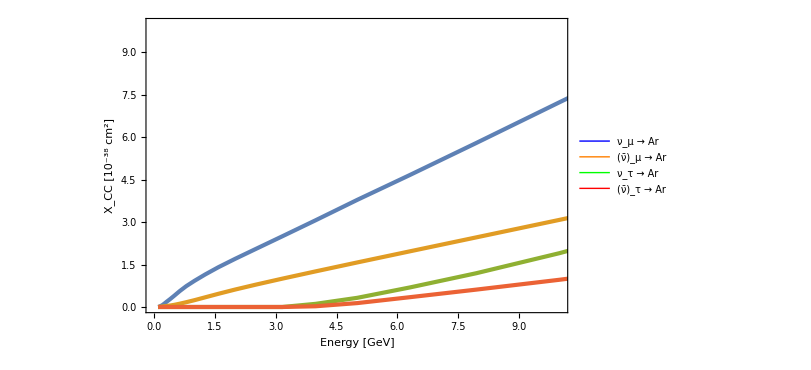

```mathematica
Show[xsec,Epilog->Text[grid,{2.0,7.0}]]
```

```mathematica
flux=Import["/Users/gstenico/Desktop/GLOBES/globes-3.2.17/DUNE/DUNE_GLoBES_Configs/flux.dat","Table"];
fnumu=Table[{flux[[i,1]],flux[[i,2]]},{i,1,Length[flux]}];
fanumu=Table[{flux[[i,1]],flux[[i,4]]},{i,1,Length[flux]}];
fnue=Table[{flux[[i,1]],flux[[i,3]]},{i,1,Length[flux]}];
fanue=Table[{flux[[i,1]],flux[[i,5]]},{i,1,Length[flux]}];
```

```mathematica
flx=ListPlot[{fnumu,fanumu,fnue,fanue},PlotRange->{{0,10},{0,120}},Frame->True,Joined->True,Frame-> True,FrameLabel-> {{"ϕ [ν/GeV/m^2/POT]",None},{"Energy [GeV]",None}},FrameStyle->Thick, LabelStyle->{Black,Bold,18},
FrameTicksStyle-> Directive[Black,18,Thick],PlotStyle->Thickness[0.005],
ImageSize-> 600];
grid2=Grid[{
{Graphics[{EdgeForm[Black],Directive[Opacity[1,Blue]],Line[{{0,0},{1,0}}]},ImageSize->20],Style["ϕ_ν_μ",14,Black]},
{Graphics[{EdgeForm[Black],Directive[Opacity[1,Orange]],Line[{{0,0},{1,0}}]},ImageSize->20],Style["ϕ_((ν̄)_μ)",14,Black]},{Graphics[{EdgeForm[Black],Directive[Opacity[1,Green]],Line[{{0,0},{1,0}}]},ImageSize->20],Style["ϕ_ν_e",14,Black]},
{Graphics[{EdgeForm[Black],Directive[Opacity[1,Red]],Line[{{0,0},{1,0}}]},ImageSize->20],Style["ϕ_((ν̄)_e)",14,Black]}
},Frame->True,Background-> White,Alignment->Left];
```

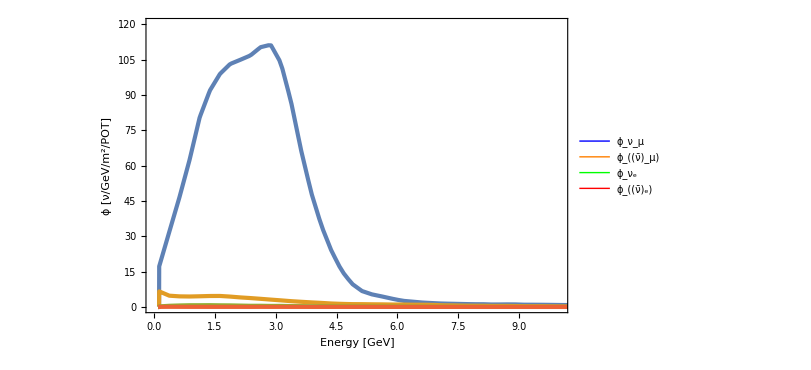

```mathematica
Show[flx,Epilog->Text[grid2,{8.0,80.0}]]
```

```mathematica
prob=Import["/Users/gstenico/Desktop/GLOBES/globes-3.2.17/DUNE/DUNE_GLoBES_Configs/pmutau.dat","Table"];
pnumu=Table[{prob[[i,1]],prob[[i,2]]},{i,1,Length[prob]}];
panumu=Table[{prob[[i,1]],prob[[i,3]]},{i,1,Length[prob]}];
pnue=Table[{prob[[i,1]],prob[[i,4]]},{i,1,Length[prob]}];
panue=Table[{prob[[i,1]],prob[[i,5]]},{i,1,Length[prob]}];
```

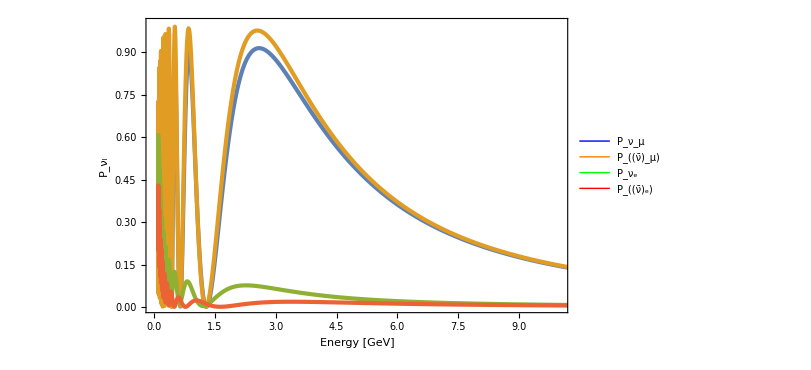

```mathematica
prb=ListPlot[{pnumu,panumu,pnue,panue},PlotRange->{{0,10},{0,1}},Frame->True,Joined->True,Frame-> True,FrameLabel-> {{"P_ν_l",None},{"Energy [GeV]",None}},FrameStyle->Thick, LabelStyle->{Black,Bold,18},
FrameTicksStyle-> Directive[Black,18,Thick],PlotStyle->Thickness[0.005],
ImageSize-> 600];
grid3=Grid[{
{Graphics[{EdgeForm[Black],Directive[Opacity[1,Blue]],Line[{{0,0},{1,0}}]},ImageSize->20],Style["P_ν_μ",14,Black]},
{Graphics[{EdgeForm[Black],Directive[Opacity[1,Orange]],Line[{{0,0},{1,0}}]},ImageSize->20],Style["P_((ν̄)_μ)",14,Black]},{Graphics[{EdgeForm[Black],Directive[Opacity[1,Green]],Line[{{0,0},{1,0}}]},ImageSize->20],Style["P_ν_e",14,Black]},
{Graphics[{EdgeForm[Black],Directive[Opacity[1,Red]],Line[{{0,0},{1,0}}]},ImageSize->20],Style["P_((ν̄)_e)",14,Black]}
},Frame->True,Background-> White,Alignment->Left]; 
Show[prb,Epilog->Text[grid3,{8.0,0.7}]]
```

```mathematica
event=Import["/Users/gstenico/Desktop/GLOBES/globes-3.2.17/SBND/sig-bg-SBND/lar-m-sig.dat","Table"];
```

```mathematica
binlar={0.2,0.35,0.5,0.65,0.8,0.95,1.1,1.3,1.5,1.75,2.,3.};
binmu={0.2,0.30,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.0,1.25,1.5,2.0,2.50,3.0};
hist=ListLinePlot[histCrea[Table[event[[i,3]]/event[[i,2]],{i,1,Length[event]}],binmu],PlotStyle->Red];
```

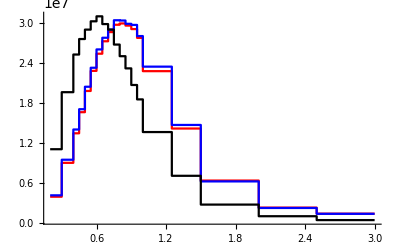

```mathematica
Show[{hist,evmu,diglar},PlotRange-> All]
```

```mathematica
larmu=Import["/Users/gstenico/Desktop/GLOBES/globes-3.2.17/SBND/lar-mu.dat","Table"];
evmu=ListLinePlot[histCrea[Table[0.11(larmu[[i,2]]*larmu[[i,3]]*larmu[[i,4]])(*/larmu[[i,5]]*),{i,1,Length[larmu]}],binmu],PlotStyle->Blue];
```

```mathematica
larmu2=Import["/Users/gstenico/Desktop/nu-LED/ev-rates/nu-mu-dis-LAR.dat","Table"];
diglar=ListLinePlot[histCrea[Table[16*larmu2[[i,2]],{i,1,Length[larmu2]}],binmu],PlotStyle->Black];
```

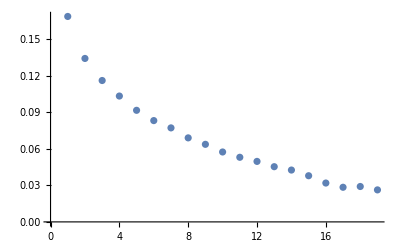

```mathematica
ListPlot[{0.168684,0.134205,0.116093,0.103341,0.0916223,0.0831809,0.0771912,0.068994,0.0636922,0.0574041,0.0530515,0.0496703,0.0453315,0.0425757,0.0379051,0.0319058,0.028431,0.029067,0.0262853}]
```

```mathematica
event=Import["/Users/gstenico/Desktop/GLOBES/globes-3.2.17/SBND/ev1_LED.dat","Table"];
event2=Import["/Users/gstenico/Desktop/GLOBES/globes-3.2.17/SBND/ev2_LED.dat","Table"];
event3=Import["/Users/gstenico/Desktop/GLOBES/globes-3.2.17/SBND/ev3_LED.dat","Table"];
```

```mathematica
binlar={0.2,0.35,0.5,0.65,0.8,0.95,1.1,1.3,1.5,1.75,2.,3.};
binmu={0.2,0.30,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.0,1.25,1.5,2.0,2.50,3.0};
hist=ListLinePlot[histCrea[Table[event[[i,3]]/event[[i,2]],{i,1,Length[event]}],binmu],PlotStyle->Red];
hist2=ListLinePlot[histCrea[Table[event2[[i,3]]/event2[[i,2]],{i,1,Length[event2]}],binmu],PlotStyle->Blue];
hist3=ListLinePlot[histCrea[Table[event3[[i,3]]/event3[[i,2]],{i,1,Length[event3]}],binmu],PlotStyle->Black];
```

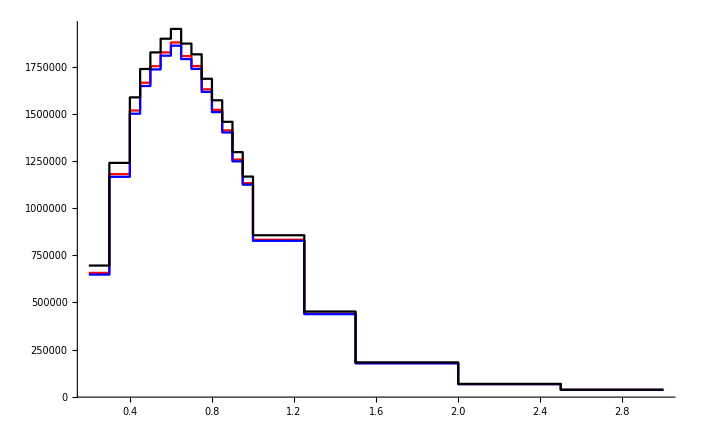

```mathematica
Show[{hist,hist2,hist3},PlotRange-> All]
```

```mathematica
|
```